```mathematica
?Graphics
```

Graphics[primitives,options] represents a two-dimensional graphical image.



```mathematica
Graphics[Circle[{-1,4},5]]
```



```mathematica
Graphics[Disk[{-1,4},5]]
```

```mathematica
?Line
```

Line[{pt_1,pt_2,…}] is a graphics primitive that represents a line joining a sequence of points. 
Line[{{pt_11,pt_12,…},{pt_21,…},…}] represents a collection of lines.

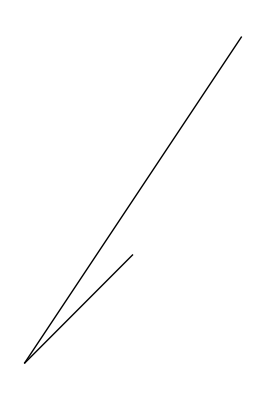

```mathematica
Graphics[{Line[{{0,0},{1,1}}],Line[{{0,0},{2,3}}]}]
```

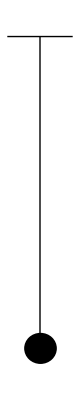

```mathematica
Graphics[{Line[{{0,0},{0,-1}}],Disk[{0,-1},0.05],Line[{{-0.1,0},{0.1,0}}]}]
```

```mathematica
Animate[Graphics[Disk[{5Cos[Pi/3]t,5Sin[Pi/3]t-1/2*9.8*t^2},0.05]],{t,0,1}]
```

```mathematica
Animate[Graphics[Disk[{5Cos[Pi/4]t,5Sin[Pi/3]t-1/2*9.8*t^2},0.05],PlotRange->{{0,4.5},{0,1}}],{t,0,1}]
```

```mathematica
s
```